Load the package.

```mathematica
<<VFD`
```

Produce a simple plot.

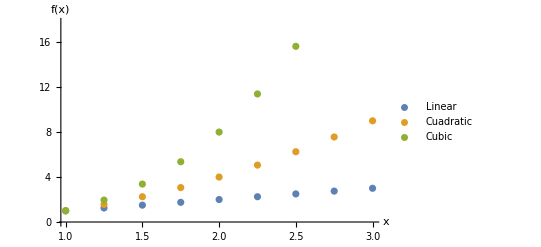

```mathematica
plot=ListPlot[Table[{x,x^k},{k,1,3},{x,1,3,0.25}],PlotLegends->{"Linear","Cuadratic","Cubic"},AxesLabel->{"x","f(x)"}]
```

Produce VFDs with the same syntax and from the plot itself.

```mathematica
vfd=CreateVFD[Table[{x,x^k},{k,1,3},{x,1,3,0.25}],PlotLegends->{"Linear","Cuadratic","Cubic"},AxesLabel->{"x","f(x)"}];
```

```mathematica
vfd2=PlotToVFD[plot];
```

```mathematica
vfd===vfd2
```

True

Open the files with vfd.

```mathematica
PreviewVFD["test.pdf",vfd2]
```

Directly export with matplotlib.

```mathematica
ExportVFD["test.pdf",vfd]
```

test.pdf